## Import Utils

```mathematica
Get["D:\\Documents\\workspace\\课题\\workspace\\Local\\Public\\mathematica\\PN_inverse\\InversePNUtils.nb"];
```

```mathematica
(*NotebookEvaluate["D:\\Documents\\workspace\\课题\\PN_inverse\\InversePNUtils.nb"]*)
```

```mathematica
NotebookEvaluate["D:\\Documents\\workspace\\课题\\workspace\\Local\\Public\\mathematica\\PN_inverse\\InversePNUtils.nb"];
```

输入Mc范围：{8,15}

输入q范围：{1,20}

m1范围：{9.18959,91.4002}

m2范围：{2.43734,17.2305}

输入Mc范围：{6,13}

输入q范围：{1,7}

m1范围：{6.89219,42.9142}

m2范围：{2.8295,14.9331}

全局极小值结果：{0.,{m1→3.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极大值结果：{0.,{m1→3.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极小值结果：{2.81559×10^-11,{m1→46.8969,m2→60.4341,spin1z→0.435746,spin2z→-0.638885}}

全局极大值结果：{8.65708,{m1→100.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极小值结果：{8.47209×10^-10,{m1→60.1419,m2→76.87,spin1z→0.320417,spin2z→-0.443897}}

全局极大值结果：{1.94773,{m1→100.,m2→3.,spin1z→0.99,spin2z→0.99}}

### Read from CSV

```mathematica
(* ==================配置==================*)
baseDir="D:\\Documents\\workspace\\课题\\workspace\\Local\\Parameterized_PN_Tests\\csv";
eventID="GW170608";

(*键名直接用短名，里面加上下划线*)
inspiralParams={"dphi_0","dphi_2","dphi_3","dphi_4","dphi_5l","dphi_6","dphi_6l","dphi_7"};
intermediateParams={"dbeta_2","dbeta_3"};
mergerParams={"dalpha_2","dalpha_3","dalpha_4"};

allParams=Join[inspiralParams,intermediateParams,mergerParams];

(* ==================读取函数==================*)
readDeviationFile[shortName_]:=Module[{path,raw},(*短名拼接上 _IMRP_posterior 还原成完整文件名*)path=FileNameJoin[{baseDir,eventID,shortName<>"_IMRP_posterior.csv"}];
raw=Import[path];
(*提取前五列*){raw[[2;;,1]],(*m1*)raw[[2;;,2]],(*m2*)raw[[2;;,3]],(*spin1z*)raw[[2;;,4]],(*spin2z*)raw[[2;;,5]]  (*偏差参数值*)}]

(*批量读取，键名就是传入的 shortName*)
readAllDeviations[]:=AssociationMap[readDeviationFile,allParams]

(* ==================执行==================*)
samples=readAllDeviations[];

(* ==================用法示例==================*)
(*直接用短名取值*)
dphi0vals=samples["dphi_0"][[5]];
dalpha3vals=samples["dalpha_3"][[5]];
```

## Calculate GR pars and further Transform $\delta$ into parameterized pars

```mathematica
(*批量计算非自旋 GR 系数值*)getGRValues[paramName_,m1s_,m2s_,chi1Ls_,chi2Ls_]:=Module[{etas},etas=etaFromMasses[m1s,m2s];
Switch[paramName,
(* =====Alpha (并合段)=====*)
"dalpha_2",IMRPhenomDAlpha[2,m1s,m2s,chi1Ls,chi2Ls],
"dalpha_3",IMRPhenomDAlpha[3,m1s,m2s,chi1Ls,chi2Ls],
"dalpha_4",IMRPhenomDAlpha[4,m1s,m2s,chi1Ls,chi2Ls],
(* =====Beta (过渡段)=====*)
"dbeta_2",IMRPhenomDBeta[2,m1s,m2s,chi1Ls,chi2Ls],
"dbeta_3",IMRPhenomDBeta[3,m1s,m2s,chi1Ls,chi2Ls],
(* =====Phi (旋近段)=====因为设置了 Listable，直接把整个 m1s,m2s 列表传进去即可，内部会自动对每个元素计算并返回列表*)
"dphi_0",IMRPhenomDPhiNS[0,m1s,m2s,0,0],
"dphi_2",IMRPhenomDPhiNS[2,m1s,m2s,0,0],
"dphi_3",IMRPhenomDPhiNS[3,m1s,m2s,0,0],
"dphi_4",IMRPhenomDPhiNS[4,m1s,m2s,0,0],
"dphi_5l",IMRPhenomDPhiLNS[5,m1s,m2s,0,0],
"dphi_6",IMRPhenomDPhiNS[6,m1s,m2s,0,0],
"dphi_6l",IMRPhenomDPhiLNS[6,m1s,m2s,0,0],
"dphi_7",IMRPhenomDPhiNS[7,m1s,m2s,0,0],
_,ConstantArray[0,Length[m1s]]
]
];

(* ==========对所有参数追加第6列(GR值)和第7列(参数化值)==========*)
Do[Module[{grVals,paramVals},
(*第6列：非自旋 GR 系数值*)grVals=getGRValues[p,samples[p][[1]],samples[p][[2]],samples[p][[3]],samples[p][[4]]];
(*第7列：参数化值=GR×(1+d)*)paramVals=grVals*(1+samples[p][[5]]);
(*拼接到原来的5列后面*)samples[p]=Join[samples[p],{grVals,paramVals}];
],{p,allParams}];
```

```mathematica
samples["dalpha_3"][[6]]
```

## m1-m2 Plot, 22

```mathematica
plots=<||>;
compPlots=<||>;
evolPlots=<||>
vsPlots=<||>;
vsPlots["p2p4"]={};
```

<||>

## INSPIRAL

### phi_2

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_2"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{3,40},{1,5}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.0417};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]},"",True][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{3,40}

输入q范围：{1,5}

m1范围：{3.4461,108.963}

m2范围：{1.63444,45.9479}

对称数据：原始 21950 + 镜像 21950

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 0.999999（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{1.63444, 108.963} × {1.63444, 108.963}

等高线值：{0.0417}，共 2 条

第一条前3点：{{8.83747,8.50305},{8.83773,8.50233},{8.85351,8.4865}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

[合并模式] 将 1 个片段强制合并为一个多边形进行积分...

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: True)

区域内总积分值：0.407821

可信水平百分比：40.7821%

==========================

dphi_2 预处理完成，红线包含概率 prob = 0.407821

```mathematica
ListLinePlot[contourPoints[p]]
```

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

```mathematica
compPlots[p]
```

```mathematica
evolPlots=<||>
```

<||>

====== [dphi_2] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.29609, 0.70391}

实际使用的 GR 概率区间上下界: {6.28621, 6.42174}

实际使用的 Param 概率区间上下界: {5.4752, 6.29954}

GR下界: 点数=1100 | Y>0点数=1100 | 平均误差=1.47761×10^-16

GR上界: 点数=1100 | Y>0点数=1100 | 平均误差=8.43769×10^-16

Param下界: 点数=1100 | Y>0点数=1100 | 平均误差=1.62294×10^-16

Param上界: 点数=1100 | Y>0点数=1100 | 平均误差=9.62462×10^-16

{{5.01,43.9672},{5.02,44.055},{5.03,44.1427},{5.04,44.2305},{5.05,44.3182}}

{{5.01,9.41033},{5.02,9.42911},{5.03,9.4479},{5.04,9.46668},{5.05,9.48546}}

chi1L取值：0.367177

chi2L取值：0.405346

=====================================================

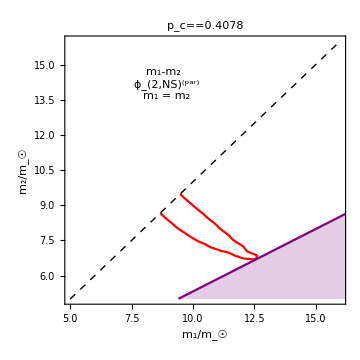

```mathematica
probability=prob;
(*probability=0.37;*)

evolPlots["at"]=PlotInversion[p,probability,5,16,0.01,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]}]
```

### phi_4

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_4"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{3,40},{1,10}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.0422};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]},"",True][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{3,40}

输入q范围：{1,10}

m1范围：{3.4461,162.307}

m2范围：{1.21731,45.9479}

对称数据：原始 16716 + 镜像 16716

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{1.21731, 162.307} × {1.21731, 162.307}

等高线值：{0.0422}，共 2 条

第一条前3点：{{9.10054,8.59714},{9.13869,8.52706},{9.24582,8.43496}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

[合并模式] 将 1 个片段强制合并为一个多边形进行积分...

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: True)

区域内总积分值：0.344313

可信水平百分比：34.4313%

==========================

dphi_4 预处理完成，红线包含概率 prob = 0.344313

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

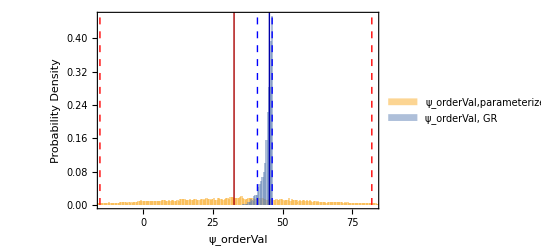

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dphi_4] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.327843, 0.672157}

实际使用的 GR 概率区间上下界: {44.5153, 45.7733}

实际使用的 Param 概率区间上下界: {20.2546, 44.3589}

GR下界: 点数=170 | Y>0点数=170 | 平均误差=4.59763×10^-15

GR上界: 点数=170 | Y>0点数=170 | 平均误差=1.11597×10^-14

Param下界: 点数=170 | Y>0点数=170 | 平均误差=9.84867

Param上界: 点数=170 | Y>0点数=170 | 平均误差=5.55895×10^-15

{{3.1,1.69529×10^6},{3.2,1.74997×10^6},{3.3,1.80466×10^6},{3.4,1.85935×10^6},{3.5,1.91402×10^6}}

{{3.1,6.00369},{3.2,6.19736},{3.3,6.39103},{3.4,6.58469},{3.5,6.77836}}

chi1L取值：0.37315

chi2L取值：0.473781

=====================================================

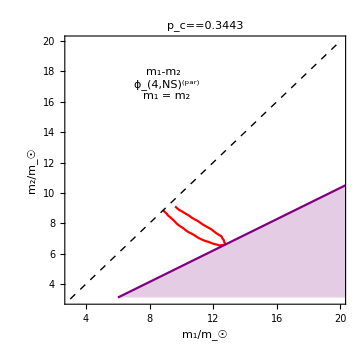

```mathematica
probability=prob;
(*probability=0.35;*)

PlotInversion[p,probability,3,20,0.1,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2}]
```

### phi_5l

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_5l"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{3,20},{1,3}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.063515};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]},"",True][[1]][[2]];
(*prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],contourPoints[p],"",False][[1]][[2]];
Print[p," 预处理完成，红线包含概率 prob = ",prob];*)
```

输入Mc范围：{3,20}

输入q范围：{1,3}

m1范围：{3.4461,40.9535}

m2范围：{2.04767,22.974}

对称数据：原始 19084 + 镜像 19084

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 40.9535} × {2.04767, 40.9535}

等高线值：{0.063515}，共 2 条

第一条前3点：{{8.76434,8.88592},{8.75347,8.89883},{8.73039,8.92623}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

[合并模式] 将 1 个片段强制合并为一个多边形进行积分...

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: True)

区域内总积分值：0.284156

可信水平百分比：28.4156%

==========================

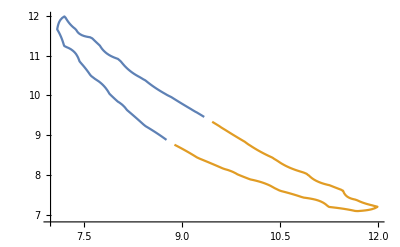

```mathematica
ListLinePlot[contourPoints[p]]
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

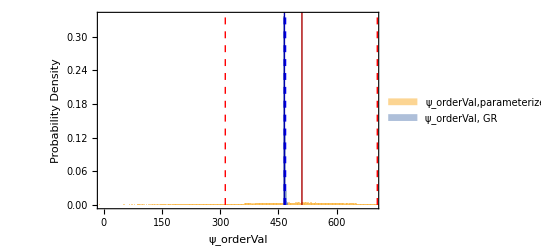

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dphi_5l] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.357922, 0.642078}

实际使用的 GR 概率区间上下界: {465.07, 465.882}

实际使用的 Param 概率区间上下界: {465.825, 552.911}

GR下界: 点数=100 | Y>0点数=100 | 平均误差=5.79803×10^-14

GR上界: 点数=100 | Y>0点数=100 | 平均误差=6.13909×10^-14

Param下界: 点数=100 | Y>0点数=100 | 平均误差=3.06954×10^-14

Param上界: 点数=100 | Y>0点数=100 | 平均误差=71.1387

{{5.1,8.51064},{5.2,8.67751},{5.3,8.84439},{5.4,9.01126},{5.5,9.17814}}

{{5.1,487964.},{5.2,497534.},{5.3,507102.},{5.4,516671.},{5.5,526238.}}

chi1L取值：0.356536

chi2L取值：0.434395

=====================================================

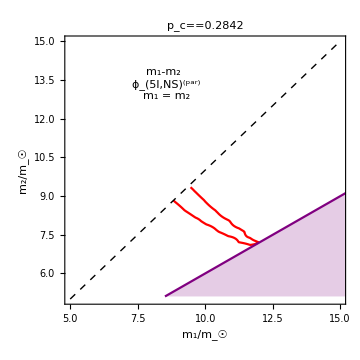

```mathematica
probability=prob;
(*probability=0.25;*)
(*probability=0.284;*)

PlotInversion[p,probability,5,15,0.1,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiLNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2}]
```

### phi_6

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_6"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{3,40},{1,5}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.0615};
contourPD[p]={0.067};
contourPD[p]={0.058};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{3,40}

输入q范围：{1,5}

m1范围：{3.4461,108.963}

m2范围：{1.63444,45.9479}

对称数据：原始 19299 + 镜像 19299

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{1.63444, 108.963} × {1.63444, 108.963}

等高线值：{0.058}，共 2 条

第一条前3点：{{8.6626,8.99801},{8.65435,9.00728},{8.60852,9.05873}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.2627

可信水平百分比：26.27%

==========================

dphi_6 预处理完成，红线包含概率 prob = 0.2627

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

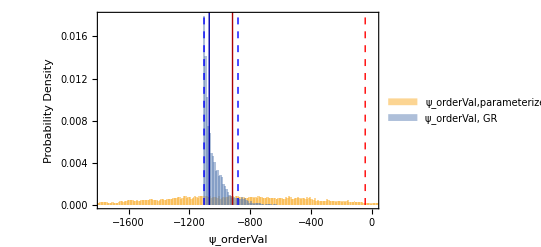

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dphi_6] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.39519, 0.60481}

实际使用的 GR 概率区间上下界: {-1082.72, -1051.46}

实际使用的 Param 概率区间上下界: {-1067.49, -769.014}

GR下界: 点数=170 | Y>0点数=170 | 平均误差=1.40437×10^-13

GR上界: 点数=170 | Y>0点数=170 | 平均误差=1.80561×10^-13

Param下界: 点数=170 | Y>0点数=170 | 平均误差=1.00312×10^-13

Param上界: 点数=170 | Y>0点数=170 | 平均误差=6.15246×10^-14

{{3.1,2.02149},{3.2,2.0867},{3.3,2.15191},{3.4,2.21712},{3.5,2.28233}}

{{3.1,13.9829},{3.2,14.434},{3.3,14.885},{3.4,15.3361},{3.5,15.7871}}

chi1L取值：0.369909

chi2L取值：0.476348

=====================================================

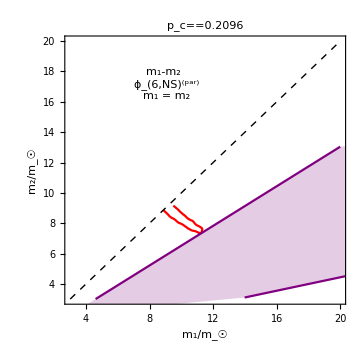

```mathematica
probability=prob;
(*probability=0.1;
*)
PlotInversion[p,probability,3,20,0.1,cm->True,cd->False,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2}]
```

====== [dphi_6] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.39519, 0.60481}

实际使用的 GR 概率区间上下界: {-1082.72, -1051.46}

实际使用的 Param 概率区间上下界: {-1067.49, -769.014}

GR下界: 点数=1700 | Y>0点数=1700 | 平均误差=1.55417×10^-13

GR上界: 点数=1700 | Y>0点数=1700 | 平均误差=1.51404×10^-13

Param下界: 点数=1700 | Y>0点数=1700 | 平均误差=1.14222×10^-13

Param上界: 点数=1700 | Y>0点数=1700 | 平均误差=7.10208×10^-14

{{3.01,1.9628},{3.02,1.96932},{3.03,1.97584},{3.04,1.98236},{3.05,1.98889}}

{{3.01,13.5769},{3.02,13.622},{3.03,13.6672},{3.04,13.7123},{3.05,13.7574}}

chi1L取值：0.369909

chi2L取值：0.476348

=====================================================

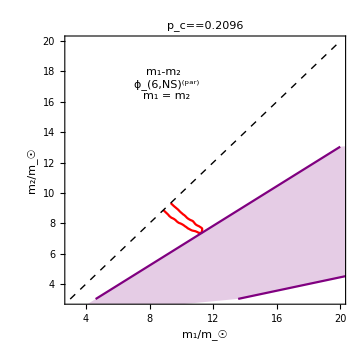

```mathematica
probability=prob;
(*probability=0.37;*)

evolPlots["at"]=PlotInversion[p,probability,3,20,0.01,cm->True,cd->False,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]}]
```

====== [dphi_6] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.43135, 0.56865}

实际使用的 GR 概率区间上下界: {-1078.95, -1059.18}

实际使用的 Param 概率区间上下界: {-1013.59, -821.238}

GR下界: 点数=1700 | Y>0点数=1700 | 平均误差=1.50735×10^-13

GR上界: 点数=1700 | Y>0点数=1700 | 平均误差=1.09407×10^-13

Param下界: 点数=1700 | Y>0点数=1700 | 平均误差=7.86445×10^-14

Param上界: 点数=1700 | Y>0点数=1700 | 平均误差=1.24788×10^-13

{{3.01,5.98929},{3.02,6.00919},{3.03,6.02909},{3.04,6.04899},{3.05,6.06889}}

{{3.01,11.5067},{3.02,11.545},{3.03,11.5832},{3.04,11.6214},{3.05,11.6596}}

chi1L取值：0.369909

chi2L取值：0.476348

=====================================================

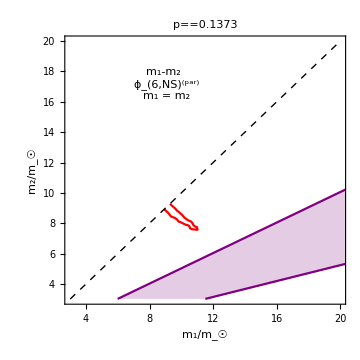

```mathematica
probability=prob;
(*probability=0.26;*)

evolPlots["before"]=PlotInversion[p,probability,3,20,0.01,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]},labelSymbol->Style["p",Italic]]
```

====== [dphi_6] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.36865, 0.63135}

实际使用的 GR 概率区间上下界: {-1085.79, -1045.9}

实际使用的 Param 概率区间上下界: {-1101.82, -731.876}

GR下界: 点数=2500 | Y>0点数=2500 | 平均误差=1.17052×10^-13

GR上界: 点数=2500 | Y>0点数=2500 | 平均误差=1.4752×10^-13

Param下界: 点数=2500 | Y>0点数=2500 | 平均误差=1.44883×10^-13

Param上界: 点数=2500 | Y>0点数=2500 | 平均误差=4.66116×10^-14

{{5.01,5.56839},{5.02,5.57951},{5.03,5.59062},{5.04,5.60173},{5.05,5.61285}}

{{5.01,25.4875},{5.02,25.5383},{5.03,25.5892},{5.04,25.6401},{5.05,25.691}}

chi1L取值：0.369909

chi2L取值：0.476348

=====================================================

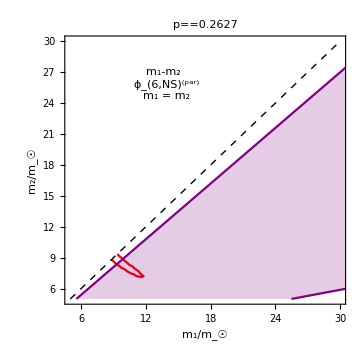

```mathematica
probability=prob;
(*probability=0.5;*)

evolPlots["after"]=PlotInversion[p,probability,5,30,0.01,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]},labelSymbol->Style["p",Italic]]
```

```mathematica
(*1. 定义你要存放 PDF 的文件夹名称*)
targetDir=FileNameJoin[{"D:\\Documents\\workspace\\课题\\论文\\fig\\",eventID}];

(*2. 如果目录不存在，则自动创建*)
If[!DirectoryQ[targetDir],CreateDirectory[targetDir];
Print["已自动创建目录: ",targetDir]];

Do[Print["正在导出矢量图: plot_",key,".pdf ..."];
Export[FileNameJoin[{targetDir,eventID<>"_dphi6_"<>key<>".pdf"}],evolPlots[key],"PDF",AllowRasterization->False (*强制全矢量输出，绝对高清*),ImageSize->500],
{key,Keys[evolPlots]}]
```

正在导出矢量图: plot_at.pdf ...

正在导出矢量图: plot_before.pdf ...

正在导出矢量图: plot_after.pdf ...

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_6"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{3,20},{1,3}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];


contourPD[p]={0.0722};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];
```

输入Mc范围：{3,20}

输入q范围：{1,3}

m1范围：{3.4461,40.9535}

m2范围：{2.04767,22.974}

对称数据：原始 19299 + 镜像 19299

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 40.9535} × {2.04767, 40.9535}

等高线值：{0.0722}，共 2 条

第一条前3点：{{9.44055,10.0769},{9.48938,10.1029},{9.51753,10.114}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：2 (合并模式: False)

区域内总积分值：0.00630729

可信水平百分比：0.630729%

==========================

dphi_6 预处理完成，红线包含概率 prob = 0.00630729

```mathematica
NMaximize[{m1m2PDF[p][x,y],5<x<20&&5<y<20},{x,y}]
```

{0.0762803,{x→8.09321,y→10.2451}}

{10.2451,8.09321}

====== [dphi_6] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.5, 0.5}

实际使用的 GR 概率区间上下界: {-1069.58, -1069.58}

实际使用的 Param 概率区间上下界: {-916.268, -916.268}

GR下界: 点数=1700 | Y>0点数=1700 | 平均误差=1.06598×10^-13

GR上界: 点数=1700 | Y>0点数=1700 | 平均误差=1.06598×10^-13

Param下界: 点数=1700 | Y>0点数=1700 | 平均误差=1.29737×10^-13

Param上界: 点数=1700 | Y>0点数=1700 | 平均误差=1.29737×10^-13

{{3.01,8.49909},{3.02,8.52733},{3.03,8.55556},{3.04,8.5838},{3.05,8.61203}}

{{3.01,8.49909},{3.02,8.52733},{3.03,8.55556},{3.04,8.5838},{3.05,8.61203}}

chi1L取值：0.369909

chi2L取值：0.476348

=====================================================

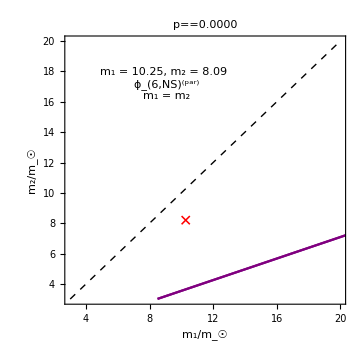

```mathematica
probability=prob;
probability=0.0;

{m1M,m2M}={10.245118127024806,8.093206815313208}

plotp0=PlotInversion[p,probability,3,20,0.01,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,
extremePoints->{{m1M,m2M}},extremePointsMarker->"Cross",extremePointsLegend->Row[{Subscript[Style["m",Italic],1]," = 10.25, ",Subscript[Style["m",Italic],2]," = 8.09"}]
,
labelSymbol->Style["p",Italic]]
```

```mathematica
(*1. 定义你要存放 PDF 的文件夹名称*)
targetDir=FileNameJoin[{"D:\\Documents\\workspace\\课题\\论文\\fig\\",eventID}];

(*2. 如果目录不存在，则自动创建*)
If[!DirectoryQ[targetDir],CreateDirectory[targetDir];
Print["已自动创建目录: ",targetDir]];


Export[FileNameJoin[{targetDir,eventID<>"_dphi6_"<>"pzero"<>".pdf"}],plotp0,"PDF",AllowRasterization->False (*强制全矢量输出，绝对高清*),ImageSize->500]
```

D:\Documents\workspace\课题\论文\fig\GW170608\GW170608_dphi6_pzero.pdf

### phi_7

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_7"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{3,40},{1,5}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.06};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{3,40}

输入q范围：{1,5}

m1范围：{3.4461,108.963}

m2范围：{1.63444,45.9479}

对称数据：原始 18147 + 镜像 18147

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{1.63444, 108.963} × {1.63444, 108.963}

等高线值：{0.06}，共 2 条

第一条前3点：{{9.0627,8.7273},{9.13896,8.66139},{9.17258,8.63233}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.178732

可信水平百分比：17.8732%

==========================

dphi_7 预处理完成，红线包含概率 prob = 0.178732

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

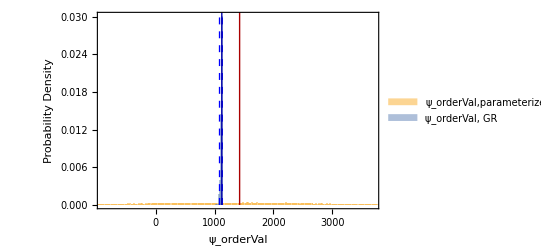

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

```mathematica
0.2927/2
```

0.14635

====== [dphi_7] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.4268, 0.5732}

实际使用的 GR 概率区间上下界: {1121.22, 1125.86}

实际使用的 Param 概率区间上下界: {1130.7, 1679.35}

GR下界: 点数=270 | Y>0点数=270 | 平均误差=4.88432×10^-14

GR上界: 点数=270 | Y>0点数=270 | 平均误差=3.3685×10^-14

Param下界: 点数=270 | Y>0点数=270 | 平均误差=3.11586×10^-14

Param上界: 点数=270 | Y>0点数=270 | 平均误差=548.456

{{3.1,2.89047},{3.2,2.98371},{3.3,3.07695},{3.4,3.17019},{3.5,3.26343}}

{{3.1,3.1001},{3.2,3.19993},{3.3,3.30007},{3.4,3.4},{3.5,3.50019}}

chi1L取值：0.365235

chi2L取值：0.434549

=====================================================

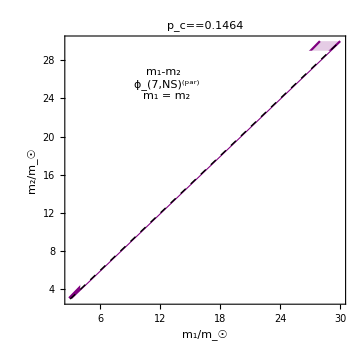

```mathematica
probability=prob;
probability=0.1464;
(*0.32*)
PlotInversion[p,probability,3,30,0.1,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{2}]
```

## Intermediate

### beta_2

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dbeta_2"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{3,40},{1,10}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.01};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]},"",True][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{3,40}

输入q范围：{1,10}

m1范围：{3.4461,162.307}

m2范围：{1.21731,45.9479}

对称数据：原始 19613 + 镜像 19613

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{1.21731, 162.307} × {1.21731, 162.307}

等高线值：{0.01}，共 2 条

第一条前3点：{{9.56886,10.0723},{9.51548,10.1301},{9.46101,10.2221}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

[合并模式] 将 1 个片段强制合并为一个多边形进行积分...

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: True)

区域内总积分值：0.855446

可信水平百分比：85.5446%

==========================

dbeta_2 预处理完成，红线包含概率 prob = 0.855446

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

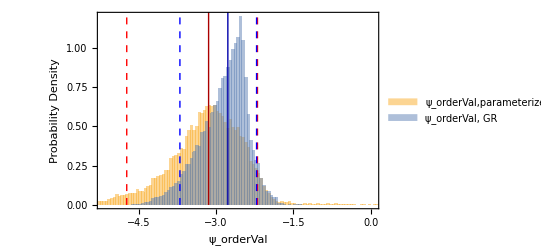

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

```mathematica
4034/2
```

2017

```mathematica
probability=prob;
probability=0.2014;

PlotInversion[p,probability,3,30,0.1,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDBeta,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1}]
```

====== [dbeta_2] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.3993, 0.6007}

实际使用的 GR 概率区间上下界: {-2.89455, -2.66454}

实际使用的 Param 概率区间上下界: {-3.312, -2.98507}

GR下界: 点数=270 | Y>0点数=270 | 平均误差=1.60201×10^-15

GR上界: 点数=270 | Y>0点数=270 | 平均误差=1.27635×10^-15

Greater::nord: Invalid comparison with 2.3587-2.0116 ⅈ attempted.

Greater::nord: Invalid comparison with 2.42892-2.08335 ⅈ attempted.

Greater::nord: Invalid comparison with 2.50458-2.14874 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Param下界: 点数=270 | Y>0点数=0 | 平均误差=0.0179404

Param上界: 点数=270 | Y>0点数=270 | 平均误差=5.05933×10^-15

{{3.1,2.3587-2.0116 ⅈ},{3.2,2.42892-2.08335 ⅈ},{3.3,2.50458-2.14874 ⅈ},{3.4,2.5804-2.21395 ⅈ},{3.5,2.65622-2.27914 ⅈ}}

{{3.1,3.09409},{3.2,3.1939},{3.3,3.29371},{3.4,3.39352},{3.5,3.49333}}

chi1L取值：0.331684

chi2L取值：0.391222

=====================================================

-Graphics-

### beta_3

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dbeta_3"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
(*{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{3,40},{1,10}];*)
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{3,40},{1,10}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.02};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]},"",True][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{3,40}

输入q范围：{1,10}

m1范围：{3.4461,162.307}

m2范围：{1.21731,45.9479}

对称数据：原始 21254 + 镜像 21254

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{1.21731, 162.307} × {1.21731, 162.307}

等高线值：{0.02}，共 2 条

第一条前3点：{{8.28261,8.78602},{8.25704,8.81856},{8.15082,8.92044}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

[合并模式] 将 1 个片段强制合并为一个多边形进行积分...

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: True)

区域内总积分值：0.769152

可信水平百分比：76.9152%

==========================

dbeta_3 预处理完成，红线包含概率 prob = 0.769152

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

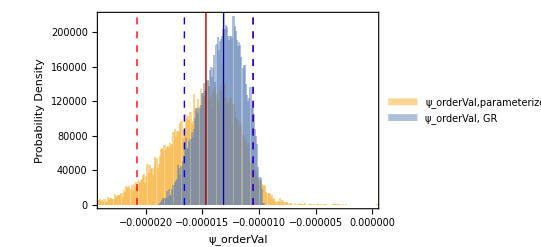

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

```mathematica
probability=prob;
probability=0.3577;
probability=0.3574;

(* 蓝色要对称一下 *)
PlotInversion[p,probability,3,20,0.1,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDBeta,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{2}]
```

====== [dbeta_3] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.3213, 0.6787}

实际使用的 GR 概率区间上下界: {-0.0000141157, -0.0000122275}

实际使用的 Param 概率区间上下界: {-0.0000162668, -0.0000133028}

Greater::nord: Invalid comparison with 0.686019+3.02314 ⅈ attempted.

Greater::nord: Invalid comparison with 0.671501+3.12875 ⅈ attempted.

Greater::nord: Invalid comparison with 0.660427+3.23324 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

GR下界: 点数=170 | Y>0点数=0 | 平均误差=4.04833×10^-7

GR上界: 点数=170 | Y>0点数=170 | 平均误差=1.4549×10^-21

Param下界: 点数=170 | Y>0点数=0 | 平均误差=7.93542×10^-21

Param上界: 点数=170 | Y>0点数=170 | 平均误差=7.26455×10^-21

{{3.1,-1.71863-4.51729 ⅈ},{3.2,-1.77407-4.66301 ⅈ},{3.3,-1.82951-4.80873 ⅈ},{3.4,-1.88495-4.95445 ⅈ},{3.5,-1.94039-5.10017 ⅈ}}

{{3.1,3.07773},{3.2,3.17701},{3.3,3.27629},{3.4,3.37557},{3.5,3.47485}}

chi1L取值：0.337847

chi2L取值：0.430621

=====================================================

-Graphics-

# Merger-RingDown

### alpha_2

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dalpha_2"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
(*{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{3,40},{1,10}];*)
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{3,40},{1,10}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.005};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{3,40}

输入q范围：{1,10}

m1范围：{3.4461,162.307}

m2范围：{1.21731,45.9479}

对称数据：原始 27748 + 镜像 27748

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{1.21731, 162.307} × {1.21731, 162.307}

等高线值：{0.005}，共 2 条

第一条前3点：{{8.64538,8.14215},{8.64485,8.14144},{8.78348,8.00272}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.95226

可信水平百分比：95.226%

==========================

dalpha_2 预处理完成，红线包含概率 prob = 0.95226

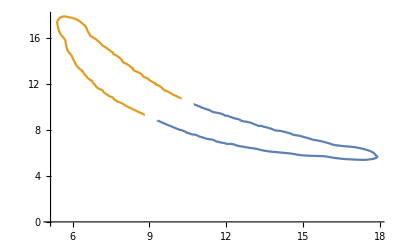

```mathematica
ListLinePlot[contourPoints[p]]
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

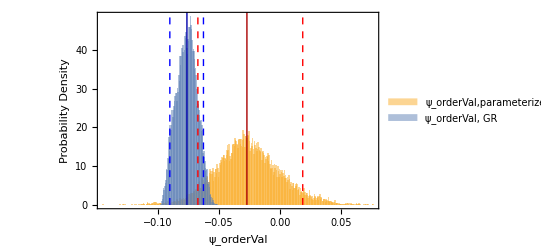

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

```mathematica
probability=prob;
probability=0.1984;
probability=0.1984;

PlotInversion[p,probability,3,60,0.1,cm->True,cd->True,cu->False,plotgr->True,projX->False,projY->False,funcName->IMRPhenomDAlpha,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{2},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]}]
```

====== [dalpha_2] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.4008, 0.5992}

实际使用的 GR 概率区间上下界: {-0.0654034, -0.0614175}

实际使用的 Param 概率区间上下界: {-1.41995, -0.065961}

GR下界: 点数=570 | Y>0点数=570 | 平均误差=3.33797×10^-17

GR上界: 点数=570 | Y>0点数=570 | 平均误差=3.11885×10^-17

Greater::nord: Invalid comparison with -6.09204-3.3842 ⅈ attempted.

Greater::nord: Invalid comparison with -6.25236-3.47326 ⅈ attempted.

Greater::nord: Invalid comparison with -6.41267-3.56232 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Param下界: 点数=570 | Y>0点数=7 | 平均误差=0.0166277

Param上界: 点数=570 | Y>0点数=570 | 平均误差=3.55223×10^-17

{{3.1,3.1},{3.2,3.2},{3.3,3.3},{3.4,3.4},{3.5,3.5}}

{{3.1,3.04534},{3.2,3.14358},{3.3,3.24182},{3.4,3.34005},{3.5,3.43829}}

chi1L取值：0.28881

chi2L取值：0.424911

=====================================================

-Graphics-

====== [dalpha_2] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.40085, 0.59915}

实际使用的 GR 概率区间上下界: {-0.0654033, -0.0614177}

实际使用的 Param 概率区间上下界: {-1.4199, -0.06601}

GR下界: 点数=570 | Y>0点数=570 | 平均误差=1.87472×10^-17

GR上界: 点数=570 | Y>0点数=570 | 平均误差=1.39143×10^-17

Param下界: 点数=570 | Y>0点数=570 | 平均误差=1.35241

Param上界: 点数=570 | Y>0点数=570 | 平均误差=2.13523×10^-17

{{3.1,4.1976},{3.2,4.32865},{3.3,4.46302},{3.4,4.6008},{3.5,4.73526}}

{{3.1,6.43108},{3.2,6.63853},{3.3,6.84598},{3.4,7.05344},{3.5,7.26089}}

chi1L取值：0.646707

chi2L取值：0.102665

=====================================================

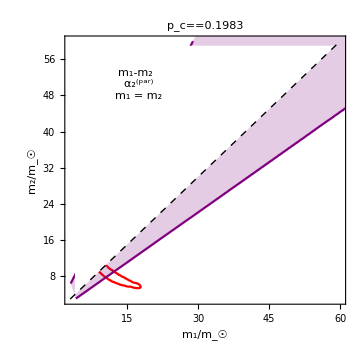

```mathematica
(*probability=prob;
probability=0.1983;

PlotInversion[p,probability,3,60,0.1,cm->True,cd->True,cu->False,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDAlpha,spinPercentile1->0.9,spinPercentile2->0.1,contourIndices->{2},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]}]*)
```

### alpha_3

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dalpha_3"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{3,30},{1,3}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.0636};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],contourPoints[p],"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

=====  =====

包含片段数：4 (合并模式: False)

区域内总积分值：0.0576862

可信水平百分比：5.76862%

==========================

dalpha_3 预处理完成，红线包含概率 prob = 0.0576862

输入Mc范围：{3,30}

输入q范围：{1,3}

m1范围：{3.4461,61.4302}

m2范围：{2.04767,34.461}

对称数据：原始 18861 + 镜像 18861

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{2.04767, 61.4302} × {2.04767, 61.4302}

等高线值：{0.0636}，共 4 条

第一条前3点：{{11.7855,7.15247},{11.7621,7.16054},{11.7485,7.16525}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

General::stop: Further output of NIntegrate::regm will be suppressed during this calculation.

=====  =====

包含片段数：4 (合并模式: False)

区域内总积分值：0.0555911

可信水平百分比：5.55911%

==========================

dalpha_3 预处理完成，红线包含概率 prob = 0.0555911

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

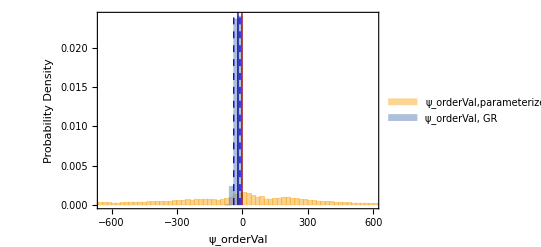

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dalpha_3] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.472204, 0.527796}

实际使用的 GR 概率区间上下界: {-20.9541, -19.8604}

实际使用的 Param 概率区间上下界: {-20.6254, 16.2306}

GR下界: 点数=170 | Y>0点数=170 | 平均误差=2.60393×10^-14

GR上界: 点数=170 | Y>0点数=170 | 平均误差=2.94666×10^-14

Param下界: 点数=170 | Y>0点数=170 | 平均误差=2.62483×10^-14

Param上界: 点数=170 | Y>0点数=170 | 平均误差=8.52461

{{3.1,1.84615},{3.2,1.9057},{3.3,1.96525},{3.4,2.02481},{3.5,2.08436}}

{{3.1,125.623},{3.2,129.703},{3.3,133.755},{3.4,137.802},{3.5,141.862}}

chi1L取值：0.366219

chi2L取值：0.431106

=====================================================

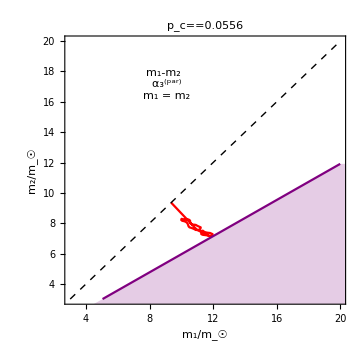

```mathematica
probability=prob;
(*probability=0.06;*)
(*probability=0.04*)
PlotInversion[p,probability,3,20,0.1,cm->True,cd->False,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDAlpha,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2,3,4}]
```

### alpha_4

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dalpha_4"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{3,20},{1,5}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.0905};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],contourPoints[p],"",False ][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{3,20}

输入q范围：{1,5}

m1范围：{3.4461,54.4814}

m2范围：{1.63444,22.974}

对称数据：原始 26622 + 镜像 26622

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{1.63444, 54.4814} × {1.63444, 54.4814}

等高线值：{0.0905}，共 4 条

第一条前3点：{{9.17323,9.00857},{9.31542,9.08267},{9.28406,9.1194}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

General::stop: Further output of NIntegrate::regm will be suppressed during this calculation.

=====  =====

包含片段数：4 (合并模式: False)

区域内总积分值：0.0011878

可信水平百分比：0.11878%

==========================

dalpha_4 预处理完成，红线包含概率 prob = 0.0011878

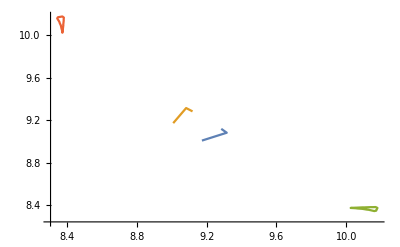

```mathematica
ListLinePlot[contourPoints[p]]
```

StringMatchQ::strse: String or list of strings expected at position 1 in StringMatchQ[orderVal,RegularExpression[^[0-9]l$]].

General::stop: Further output of StringMatchQ::strse will be suppressed during this calculation.

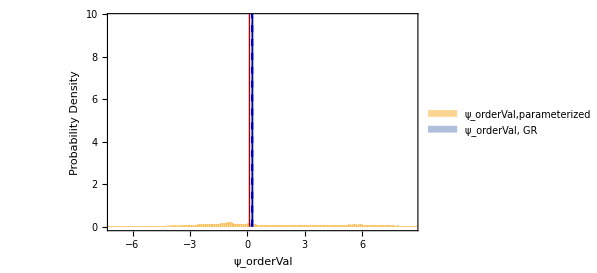

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dalpha_4] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.472346, 0.527654}

实际使用的 GR 概率区间上下界: {0.257911, 0.259712}

实际使用的 Param 概率区间上下界: {-0.139077, 0.392026}

GR下界: 点数=170 | Y>0点数=170 | 平均误差=4.37558×10^-17

GR上界: 点数=170 | Y>0点数=170 | 平均误差=4.70212×10^-17

Param下界: 点数=170 | Y>0点数=170 | 平均误差=0.138637

Greater::nord: Invalid comparison with 1.18916-2.86285 ⅈ attempted.

Greater::nord: Invalid comparison with 1.22751-2.9552 ⅈ attempted.

Greater::nord: Invalid comparison with 1.26587-3.04755 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Param上界: 点数=170 | Y>0点数=0 | 平均误差=0.000187058

{{3.1,2.34815×10^6},{3.2,2.4239×10^6},{3.3,2.49966×10^6},{3.4,2.57539×10^6},{3.5,2.65114×10^6}}

{{3.1,1.18916-2.86285 ⅈ},{3.2,1.22751-2.9552 ⅈ},{3.3,1.26587-3.04755 ⅈ},{3.4,1.30423-3.1399 ⅈ},{3.5,1.34259-3.23225 ⅈ}}

chi1L取值：0.303163

chi2L取值：0.384705

=====================================================

-Graphics-

=====================================================

chi2L取值：0.384705

chi1L取值：0.303163

Param上界: 点数=170 | 平均误差=5.74704×10^-17

Param下界: 点数=170 | 平均误差=0.0130508

GR上界: 点数=170 | 平均误差=6.7593×10^-17

GR下界: 点数=170 | 平均误差=4.14701×10^-17

实际使用的 Param 概率区间上下界: {-0.0134924, 0.250581}

实际使用的 GR 概率区间上下界: {0.258358, 0.259322}

实际使用的概率区间上下界: {0.485, 0.515}

====== [dalpha_4] 反解校验报告 (容差: 1/100000) ======

====== [dalpha_4] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.485, 0.515}

实际使用的 GR 概率区间上下界: {0.258358, 0.259322}

实际使用的 Param 概率区间上下界: {-0.0134924, 0.250581}

GR下界: 点数=170 | 平均误差=4.14701×10^-17

GR上界: 点数=170 | 平均误差=6.7593×10^-17

Param下界: 点数=170 | 平均误差=0.0130508

Param上界: 点数=170 | 平均误差=5.74704×10^-17

chi1L取值：0.303163

chi2L取值：0.384705

=====================================================

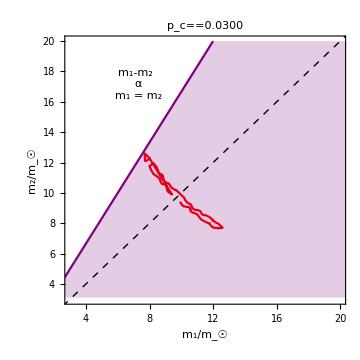

```mathematica
probability=prob;
(*probability=0.01;
probability=0.03;

*)PlotInversion[p,probability,3,20,0.1,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomDAlpha,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2,3,4,5,6,7,8}]
```

```mathematica
p
```

dalpha_4

# utils